```mathematica
Quit[]
```

```mathematica
VecToso3[omg_]:={{0,-omg[[3,1]],omg[[2,1]]},{omg[[3,1]],0,-omg[[1,1]]},{-omg[[2,1]],omg[[1,1]],0}}
TransToRp[T_]:={T[[1;;3,1;;3]],{T[[1;;3,4]]}ᵀ}
VecTose3[V_]:=ArrayFlatten[{{VecToso3[{V[[1;;3,1]]}ᵀ],{V[[4;;6,1]]}ᵀ},{0,0}}]
se3ToVec[se3mat_]:={{se3mat[[3,2]],se3mat[[1,3]],se3mat[[2,1]],se3mat[[1,4]],se3mat[[2,4]],se3mat[[3,4]]}}ᵀ
Adjoint[T_]:=Module[{R,p},{R,p}=TransToRp[T];Return[ArrayFlatten[{{R,0},{VecToso3[p].R,R}}]]]
tm[theta_,x_,y_]:= {{Cos[theta],-Sin[theta],0,x},{Sin[theta],Cos[theta],0,y},{0,0,1,0},{0,0,0,1}}
JoinInterpolatingFunction[intervals_List,flist_List]:=Module[{getGrid},getGrid[f_InterpolatingFunction,min_?NumericQ,max_?NumericQ]:={{min,f[min]}}~Join~(Transpose@{f["Grid"]//Flatten,f["ValuesOnGrid"]}//Select[#,(min<#[[1]]<max)&]&)~Join~{{max,f[max]}}//N;
Interpolation[Table[getGrid[flist[[i]],intervals[[i]],intervals[[i+1]]],{i,Length@flist}]//Flatten[#,1]&//DeleteDuplicates[#,(#1[[1]]==#2[[1]])&]&,InterpolationOrder->2]]
```

## Part {a} - With Constraint force

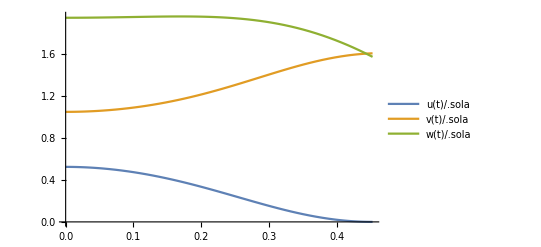

{}

```mathematica
T01=tm[u[t],0,0].tm[0,l1,0].tm[v[t],0,0].tm[0,-l4,0] //FullSimplify;
T02=tm[u[t],0,0].tm[0,-l2,0].tm[w[t]-Pi/2,0,0].tm[0,0,-l3] //FullSimplify;
T0m=tm[u[t],0,0].tm[0,-lm,0] //FullSimplify;
inzz=inyy=(3*r^2+(l1+l2)^2)/12;
inxx=r^2/2;
rad=0.3;
in=m3*DiagonalMatrix[{inxx,inyy,inzz,1,1,1}];
(*in=m3*DiagonalMatrix[{1,1,1,1,1,1}];*)
v1=se3ToVec[Inverse[T01].D[T01,t]]; 
v2=se3ToVec[Inverse[T02].D[T02,t]] ;
v3=se3ToVec[Inverse[T0m].D[T0m,t]] ;
ke= 0.5* (Transpose[v1].in.v1 + Transpose[v2].in.v2+Transpose[v3].in.v3) //FullSimplify;
pe=g*(m1*T01[[2,4]]+m2*T02[[2,4]]+m3*T0m[[2,4]]) //FullSimplify;
lag=ke-pe;

cns=T02[[2,4]]+h-rad;
cns11=D[D[cns,t],t]==0;

eq1=D[D[lag,u'[t]],t]-D[lag,u[t]]==k1*D[cns,u[t]];
eq2=D[D[lag,v'[t]],t]-D[lag,v[t]]==k1*D[cns,v[t]];
eq3=D[D[lag,w'[t]],t]-D[lag,w[t]]==k1*D[cns,w[t]];

sol1=Solve[cns11&&eq1&&eq2&&eq3,{u''[t],v''[t],w''[t],k1}];
aa=u''[t]==sol1[[1,1,2]];
bb=v''[t]==sol1[[1,2,2]];
cc=w''[t]==sol1[[1,3,2]];

(*l1=3;l2=9;l3=12;l4=3;lm=1.5;h=12;r=0;m1=30;m2=3;m3=5;*)
l1=1;l2=3;l3=4;l4=1;lm=0.5;h=4;r=0;m1=20;m2=1;m3=1;
g=9.8;
w0=ArcCos[(h-l2*Sin[Pi/6])/l3]+Pi/2-Pi/6 //N;

eq4=u[0]==Pi/6;
eq5=v[0]==Pi/2- Pi/6;
eq6=w[0]== w0;
eq7=u'[0]==0;
eq8=v'[0]==0;
eq9=w'[0]==0;

sola=NDSolve[{aa,bb,cc,eq4,eq5,eq6,eq7,eq8,eq9,WhenEvent[u[t]+w[t]==Pi/2,t1=t;"StopIntegration"]},{u,v,w},{t,0,10}];


solfinalu=List[];
solfinalv=List[];
solfinalw=List[];

solfinalu=AppendTo[solfinalu,{sola[[1,1,2]][th],0<th≤ t1}];
solfinalv=AppendTo[solfinalv,{sola[[1,2,2]][th],0<th≤ t1}];
solfinalw=AppendTo[solfinalw,{sola[[1,3,2]][th],0<th≤ t1}];



Plot[{u[t]/.sola,v[t]/.sola,w[t]/.sola},{t,0,t1},PlotLegends->"Expressions"]
a1=u[t1]/.sola;
a2=v[t1]/.sola;
a3=w[t1]/.sola;
b1=u'[t1]/.sola;
b2=v'[t1]/.sola;
b3=w'[t1]/.sola;


pa={{0,0,0,1}}ᵀ;



Animate[Show[Graphics[{Point[{0,0}],

Line[{Drop[tm[u[t],0,0].tm[0,l1,0].pa,-2]ᵀ[[1]],Drop[tm[u[t],0,0].tm[0,-l2,0].pa,-2]ᵀ[[1]] }],
Line[{Drop[tm[u[t],0,0].tm[0,l1,0].pa,-2]ᵀ[[1]],Drop[tm[u[t],0,0].tm[0,l1,0].tm[v[t],0,0].tm[0,-l4,0].pa,-2]ᵀ[[1]]}],

Line[{Drop[tm[u[t],0,0].tm[0,-l2,0].pa,-2]ᵀ[[1]],Drop[tm[u[t],0,0].tm[0,-l2,0].tm[w[t]-Pi/2,0,0].tm[0,0,-l3].pa,-2]ᵀ[[1]]}]}],
PlotRange -> {{-10,10},{10,-10}},Axes-> True,Frame-> True],{t,0,t1},AnimationRunning->False]/.sola
```

## Part {b} - No constraint

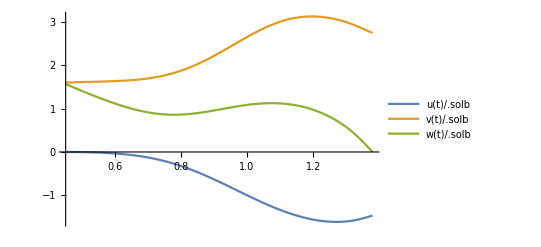

{}

```mathematica
Clear[u,v,w]
eq1=D[D[lag,u'[t]],t]-D[lag,u[t]]==0;
eq2=D[D[lag,v'[t]],t]-D[lag,v[t]]==0;
eq3=D[D[lag,w'[t]],t]-D[lag,w[t]]==0;
eq4=u[t1]==a1[[1]];
eq5=v[t1]==a2[[1]];
eq6=w[t1]== a3[[1]];
eq7=u'[t1]==b1[[1]];
eq8=v'[t1]==b2[[1]];
eq9=w'[t1]==b3[[1]];
solb=NDSolve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,WhenEvent[w[t]==0,t2=t;"StopIntegration"]},{u,v,w},{t,t1,10}];

solfinalu=AppendTo[solfinalu,{solb[[1,1,2]][th],t1<th≤ t2}];
solfinalv=AppendTo[solfinalv,{solb[[1,2,2]][th],t1<th≤ t2}];
solfinalw=AppendTo[solfinalw,{solb[[1,3,2]][th],t1<th≤ t2}];

solfinalu=AppendTo[solfinalu,{u[t2]/.solb[[1,1]],t2<th≤ 10}];
solfinalv=AppendTo[solfinalv,{v[t2]/.solb[[1,2]],t2<th≤ 10}];
solfinalw=AppendTo[solfinalw,{w[t2]/.solb[[1,3]],t2<th≤ 10}];



Plot[{u[t]/.solb,v[t]/.solb,w[t]/.solb},{t,t1,t2},PlotLegends->"Expressions"]



Animate[Show[Graphics[{Point[{0,0}],
Line[{Drop[tm[u[t],0,0].tm[0,l1,0].pa,-2]ᵀ[[1]],Drop[tm[u[t],0,0].tm[0,-l2,0].pa,-2]ᵀ[[1]] }],
Line[{Drop[tm[u[t],0,0].tm[0,l1,0].pa,-2]ᵀ[[1]],Drop[tm[u[t],0,0].tm[0,l1,0].tm[v[t],0,0].tm[0,-l4,0].pa,-2]ᵀ[[1]]}],

Line[{Drop[tm[u[t],0,0].tm[0,-l2,0].pa,-2]ᵀ[[1]],Drop[tm[u[t],0,0].tm[0,-l2,0].tm[w[t]-Pi/2,0,0].tm[0,0,-l3].pa,-2]ᵀ[[1]]}]}],
PlotRange -> {{-20,20},{20,-20}},Axes-> True,Frame-> True],{t,t1,t2},AnimationRunning->False]/.solb
```

## Part {c} - Impact of the mass

```mathematica
T0b=tm[q[t],x[t],y[t]];
vb=se3ToVec[Inverse[T0b].D[T0b,t]];
keb=1/2*mb*Transpose[vb].IdentityMatrix[6].vb;
peb=mb*g*T0b[[2,4]];

lagb=keb-peb;
eqca=D[D[lagb,q'[t]],t]-D[lagb,q[t]]==0;
eqcb=D[D[lagb,x'[t]],t]-D[lagb,x[t]]==0;
eqcc=D[D[lagb,y'[t]],t]-D[lagb,y[t]]==0;


mb=1;
Off[Solve::ratnz]
solutionq=solutiony=List[];
solutionx=List[];
cons=y[t]+2.5-rad;
imp1a=ReplaceAll[t->ta][D[lagb,q'[t]]]-ReplaceAll[t->tb][D[lagb,q'[t]]]==lam*D[cons,q[t]];
imp1b=ReplaceAll[t->ta][D[lagb,x'[t]]]-ReplaceAll[t->tb][D[lagb,x'[t]]]==lam*D[cons,x[t]];
imp1c=ReplaceAll[t->ta][D[lagb,y'[t]]]-ReplaceAll[t->tb][D[lagb,y'[t]]]==lam*D[cons,y[t]];
imp2=ReplaceAll[t->ta][D[lagb,q'[t]]*q'[t]+D[lagb,x'[t]]*x'[t]+D[lagb,y'[t]]*y'[t]-lagb]-ReplaceAll[t->tb][D[lagb,q'[t]]*q'[t]+D[lagb,x'[t]]*x'[t]+D[lagb,y'[t]]*y'[t]-lagb]==0;
solimp=Solve[imp1a&&imp1b&&imp1c&&imp2,{q'[ta],x'[ta],y'[ta],lam}]//FullSimplify;
solmat=List[];
tmat=List[];

cr=0.5;(*coefficient to account for energy loss*)

For[count=1;t0=t2;
xinit=(T02/.solb /.t-> t2 )[[1,1,4]];
yinit=(T02/.solb /.t-> t2 )[[1,2,4]];
qinit=0;
dxinit=(D[T02,t]/.solb /.t-> t2 )[[1,1,4]];
dyinit=(D[T02,t]/.solb /.t-> t2 )[[1,2,4]];
dqinit=2,
count<3,count++,
tinit=t0;
sol3=NDSolve[{eqca,eqcb,eqcc,x[t0]==xinit,y[t0]==yinit,q[t0]==qinit,q'[t0]==dqinit,x'[t0]==dxinit,y'[t0]==dyinit},{q,x,y},{t,t0,10},Method->{"EventLocator", "Event"-> y[t]+2.5-rad==0,"EventAction":>(xinit=x[t];yinit=y[t];qinit=q[t];
tb=t;
solimp1=Solve[imp1a&&imp1b&&imp1c&&imp2,{q'[ta],x'[ta],y'[ta],lam}] //FullSimplify ;
dqinit=-cr*dqinit;
dxinit=cr*solimp1[[2,2,2]]/.ta-> t;
dyinit=cr*solimp1[[2,3,2]]/.ta-> t;
t0=t;
tmat=AppendTo[tmat,t0];
"StopIntegration")}];
If[tinit==t0,t0=10];
Print[tinit," ",t0];
solmat=AppendTo[solmat,sol3];
solutionq=AppendTo[solutionq,{sol3[[1,1,2]][th],tinit<th≤ t0}];
solutionx=AppendTo[solutionx,{sol3[[1,2,2]][th],tinit<th≤ t0}];
solutiony=AppendTo[solutiony,{sol3[[1,3,2]][th],tinit<th≤ t0}];
]
```

1.37902 2.93114

2.93114 4.30969

## Part {d} - Compilation

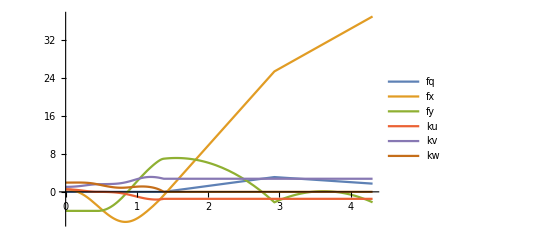

```mathematica
ku=Piecewise[solfinalu];
kv=Piecewise[solfinalv];
kw=Piecewise[solfinalw];
uu[t_]:= ku /.th-> t
vv[t_]:= kv /.th-> t
ww[t_]:= kw /.th-> t
cx=Drop[tm[uu[th],0,0].tm[0,-l2,0].tm[ww[th]-Pi/2,0,0].tm[0,0,-l3].pa,-2]ᵀ[[1,1]];
cy=Drop[tm[uu[th],0,0].tm[0,-l2,0].tm[ww[th]-Pi/2,0,0].tm[0,0,-l3].pa,-2]ᵀ[[1,2]];
finalq=Piecewise[solutionq];
finalx=Piecewise[solutionx];
finaly=Piecewise[solutiony];
fq=Piecewise[{{0,th≤ t2},{finalq,th>t2}}];
fx=Piecewise[{{cx,th≤ t2},{finalx,th>t2}}];
fy=Piecewise[{{cy,th≤ t2},{finaly,th>t2}}];
Plot[{fq,fx,fy,ku,kv,kw},{th,0,t0},PlotLegends->"Expressions",PlotRange->Full]

xx[t_]:=fx /.th-> t
yy[t_]:=fy /.th-> t
qq[t_]:=fq/.th-> t

Animate[Show[Graphics[{Point[{0,0}],
Circle[{xx[t],yy[t]},rad],Line[{Drop[tm[0,xx[t],yy[t]].tm[qq[t],0,0].tm[0,-rad,0].pa,-2]ᵀ[[1]],Drop[tm[0,xx[t],yy[t]].tm[qq[t],0,0].tm[0,rad,0].pa,-2]ᵀ[[1]] }],
Line[{Drop[tm[uu[t],0,0].tm[0,l1,0].pa,-2]ᵀ[[1]],Drop[tm[uu[t],0,0].tm[0,-l2,0].pa,-2]ᵀ[[1]] }],PointSize[0.02],Point[Drop[tm[uu[t],0,0].tm[0,l1,0].tm[vv[t],0,0].tm[0,-l4,0].pa,-2]ᵀ[[1]]],
Line[{Drop[tm[uu[t],0,0].tm[0,l1,0].pa,-2]ᵀ[[1]],Drop[tm[uu[t],0,0].tm[0,l1,0].tm[vv[t],0,0].tm[0,-l4,0].pa,-2]ᵀ[[1]]}],
Line[{Drop[tm[uu[t],0,0].tm[0,-l2,0].pa,-2]ᵀ[[1]],Drop[tm[uu[t],0,0].tm[0,-l2,0].tm[ww[t]-Pi/2,0,0].tm[0,0,-l3].pa,-2]ᵀ[[1]]}],
Opacity[0.3],Triangle[{{0,0},{-0.5,-h-rad},{0.5,-h-rad}}],Opacity[0.5],Dashed,Line[{{22,-2.5},{40,-2.5}}],Line[{{-10,-h-rad},{5,-h-rad}}]},ImageSize->1000],
PlotRange -> {{-8,40},{10,-5}}],{t,0,t0},AnimationRunning->False,RefreshRate->120]
```

```mathematica
Export["trebuchet.avi",Animate[Show[Graphics[{Point[{0,0}],
Circle[{xx[t],yy[t]},rad],Line[{Drop[tm[0,xx[t],yy[t]].tm[qq[t],0,0].tm[0,-rad,0].pa,-2]ᵀ[[1]],Drop[tm[0,xx[t],yy[t]].tm[qq[t],0,0].tm[0,rad,0].pa,-2]ᵀ[[1]] }],
Line[{Drop[tm[uu[t],0,0].tm[0,l1,0].pa,-2]ᵀ[[1]],Drop[tm[uu[t],0,0].tm[0,-l2,0].pa,-2]ᵀ[[1]] }],PointSize[0.02],Point[Drop[tm[uu[t],0,0].tm[0,l1,0].tm[vv[t],0,0].tm[0,-l4,0].pa,-2]ᵀ[[1]]],
Line[{Drop[tm[uu[t],0,0].tm[0,l1,0].pa,-2]ᵀ[[1]],Drop[tm[uu[t],0,0].tm[0,l1,0].tm[vv[t],0,0].tm[0,-l4,0].pa,-2]ᵀ[[1]]}],
Line[{Drop[tm[uu[t],0,0].tm[0,-l2,0].pa,-2]ᵀ[[1]],Drop[tm[uu[t],0,0].tm[0,-l2,0].tm[ww[t]-Pi/2,0,0].tm[0,0,-l3].pa,-2]ᵀ[[1]]}],
Opacity[0.3],Triangle[{{0,0},{-0.5,-h-rad},{0.5,-h-rad}}],Opacity[0.5],Dashed,Line[{{22,-2.5},{40,-2.5}}],Line[{{-10,-h-rad},{5,-h-rad}}]},ImageSize->100],
PlotRange -> {{-8,40},{10,-5}}],{t,0,t0},AnimationRunning->False,RefreshRate->120],"FrameRate"-> 60]
```

trebuchet.avi